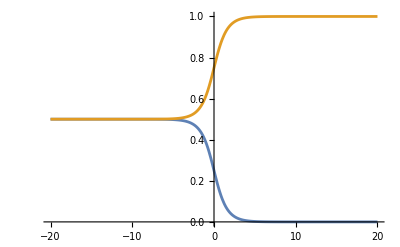

```mathematica
Plot[{ArcCot[E^x]/Pi,1 -ArcCot[E^x]/Pi},{x,-20,20}]
```

```mathematica
(*
r0=np.log(np.tan(pi/q))
r1=np.log(np.tan(pi(q-2)/(2*q)))
p=np.floor(q/pi*np.arctan(np.exp(-r0-np.random.random()*(r1-r0))))
if np.random.random()<0.5:p=q-p
if gcd(p,q)==1:# P((p,q)=1)=phi(q)/q
pass
*)
```

```mathematica
QP[q_] :=
Block[{r0,r1,p},
r0 = Log[Tan[Pi/q]];
r1 = Log[Tan[Pi(q/2-1)/q]];
 p =Floor[q/Pi ArcTan[Exp[-r0 - RandomReal[](r1-r0)]]];
If[RandomInteger[]==1, p = q -p] ;
{q,p}
]
```

```mathematica
qp = Transpose[QP[Table[2*RandomInteger[{2, 100000000}],10000]]];
```

```mathematica
Dimensions[qp]
```

{10000,2}

```mathematica
test=Select[qp,GCD[#[[1]],#[[2]]]==1&];
```

```mathematica
Length[test]
```

4079

```mathematica
test[[;;10]]
```

{{3520256,53},{161800432,161},{192919496,169},{92788218,137},{175423766,165},{118878388,147},{25958248,95},{29567644,99},{67131814,125},{191050490,169}}

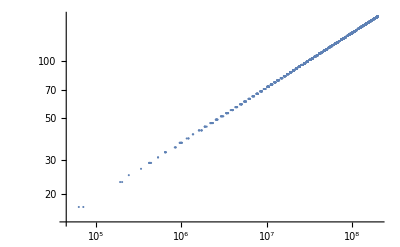

```mathematica
ListLogLogPlot[test]
```

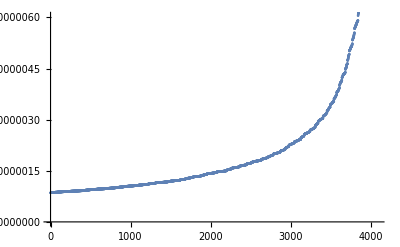

```mathematica
ListPlot[Sort[N[#[[2]]/#[[1]]]& /@ test]]
```

```mathematica
ltest = Sort[N[Cot[Pi #[[2]]/#[[1]]]]& /@ test];
```

```mathematica
N[{ltest[[1]],ltest[[-1]]}]
```

{1173.66,372289.}

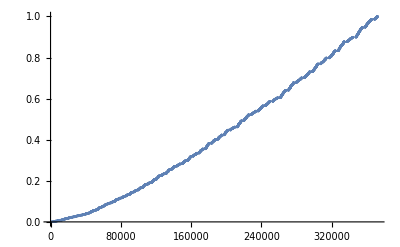

```mathematica
ListPlot[Transpose[{ltest, Range[Length[ltest]]/Length[ltest]}]]
```

```mathematica
ltest1 =Sort[N[Log[Cot[Pi #[[2]]/#[[1]]]]]& /@ test];
```

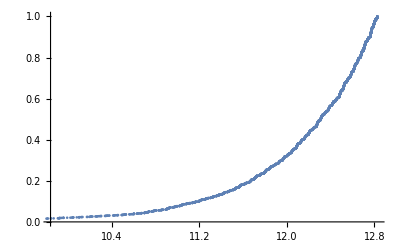

```mathematica
ListPlot[Transpose[{ltest1,Range[Length[ltest1]]/Length[ltest1]}]]
```

```mathematica
""
```